```mathematica
k=(kx^2+ky^2)^(1/2)
Ω=(kx^2+ky^2+I*ρ*ω/μ)^(1/2)
ux[x_,y_,z_,t_]=(Ax*Exp[Ω*z]+Bx*Exp[-Ω*z]-A*kx/ω*Exp[k*z]-B*kx/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uy[x_,y_,z_,t_]=(Ay*Exp[Ω*z]+By*Exp[-Ω*z]-A*ky/ω*Exp[k*z]-B*ky/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
uz[x_,y_,z_,t_]=(Az*Exp[Ω*z]+Bz*Exp[-Ω*z]+I*A*k/ω*Exp[k*z]-I*B*k/ω*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
P[x_,y_,z_,t_]=-g*z+(A*Exp[k*z]+B*Exp[-k*z])*Exp[I*(kx*x+ky*y+ω*t)]
h[x_,y_,z_,t_]=h0+H*Exp[I*(kx*x+ky*y+ω*t)]
```

√(kx^2+ky^2)

√(kx^2+ky^2+(ⅈ ρ ω)/μ)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bx ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ax ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) kx)/ω-(A ⅇ^(√(kx^2+ky^2) z) kx)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (By ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Ay ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(B ⅇ^(-√(kx^2+ky^2) z) ky)/ω-(A ⅇ^(√(kx^2+ky^2) z) ky)/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (Bz ⅇ^(-z √(kx^2+ky^2+(ⅈ ρ ω)/μ))+Az ⅇ^(z √(kx^2+ky^2+(ⅈ ρ ω)/μ))-(ⅈ B ⅇ^(-√(kx^2+ky^2) z) √(kx^2+ky^2))/ω+(ⅈ A ⅇ^(√(kx^2+ky^2) z) √(kx^2+ky^2))/ω)

ⅇ^(ⅈ (kx x+ky y+t ω)) (B ⅇ^(-√(kx^2+ky^2) z)+A ⅇ^(√(kx^2+ky^2) z))-g z

ⅇ^(ⅈ (kx x+ky y+t ω)) H+h0

```mathematica
Expand[D[ux[x,y,z,t],t]-μ/ρ*(D[ux[x,y,z,t],{x,2}]+D[ux[x,y,z,t],{y,2}]+D[ux[x,y,z,t],{z,2}])+D[P[x,y,z,t],x]]
Expand[D[uy[x,y,z,t],t]-μ/ρ*(D[uy[x,y,z,t],{x,2}]+D[uy[x,y,z,t],{y,2}]+D[uy[x,y,z,t],{z,2}])+D[P[x,y,z,t],y]]
Expand[D[uz[x,y,z,t],t]-μ/ρ*(D[uz[x,y,z,t],{x,2}]+D[uz[x,y,z,t],{y,2}]+D[uz[x,y,z,t],{z,2}])+D[P[x,y,z,t],z]+g]
```

0

0

0

#### flat

```mathematica
subs0={A->KroneckerDelta[k1,1],B->KroneckerDelta[k1,2],Ax->KroneckerDelta[k1,3],Bx->KroneckerDelta[k1,4],Ay->KroneckerDelta[k1,5],By->KroneckerDelta[k1,6],Az->KroneckerDelta[k1,7],Bz->KroneckerDelta[k1,8], H->KroneckerDelta[k1,9],kx->qx,ky->qy,ω->ω+l1*ωd};
eqs0=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs0],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs0],Simplify[(I*kx*uz[x,y,z,t]-(D[ux[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs0],Simplify[(I*ky*uz[x,y,z,t]-(D[uy[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs0],Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0],Simplify[ux[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uy[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[uz[x,y,z,t]*Exp[-I*(kx*x+ky*y+ω*t)]/.z->0/.subs0],Simplify[(-g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs0]},{k1,1,9}]];
```

```mathematica
M=3;
eq0=Simplify[(eqs0[[9;;9,9;;9]]-eqs0[[9;;9,1;;8]].Inverse[eqs0[[1;;8,1;;8]]].eqs0[[1;;8,9;;9]])[[1,1]]/.qy->0];
eq1=Table[eq0*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}];
eq2=Table[-1/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]),{l1,-M,M},{l2,-M,M}];
```

```mathematica
freq=2*Pi*23.;
sys={eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]
evals
```

{0.00024,Null}

{ComplexInfinity,-78562.2+11.4568 ⅈ,78562.2-11.4568 ⅈ,-20996.9+0.192308 ⅈ,20996.9-0.192308 ⅈ,-45.4782+8.06057×10^-14 ⅈ,45.4782-7.73413×10^-14 ⅈ}

```mathematica
AbsoluteTiming[vals=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.1/.ρ->1/.h0->1/.ωd->freq/.ω->ϵ*freq],{ϵ,-1,1,1/100}];]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of Eigenvalues::mindet will be suppressed during this calculation.

{3.18464,Null}

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

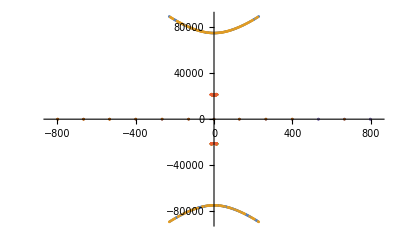

```mathematica
ListPlot[Transpose[{Im[#],Re[#]}&/@#&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]],Joined->False]
```

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

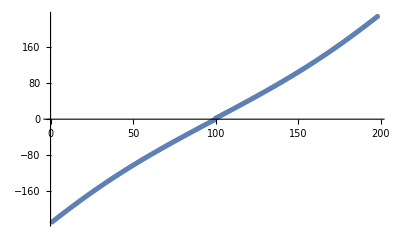
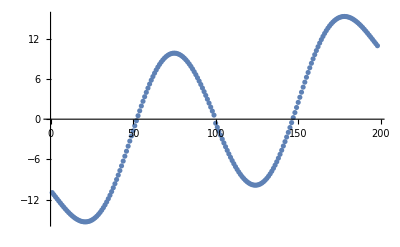
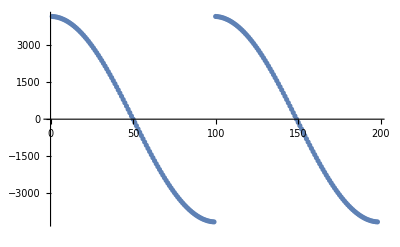
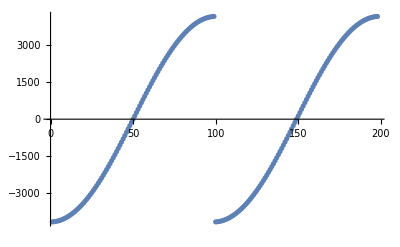
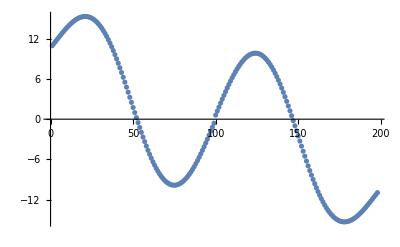
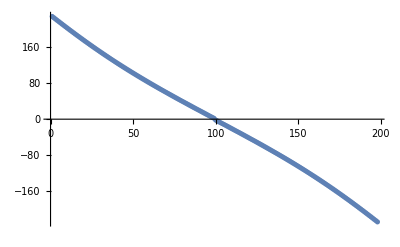

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

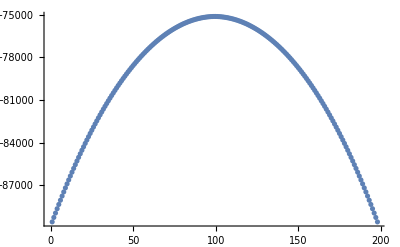
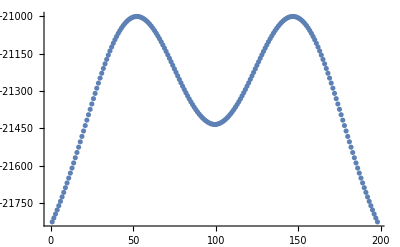
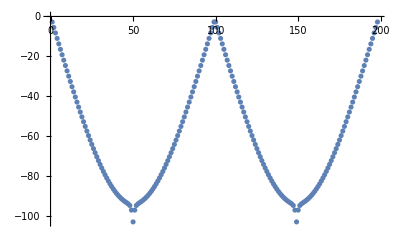
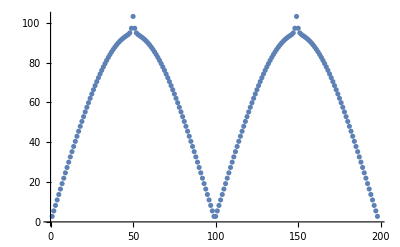
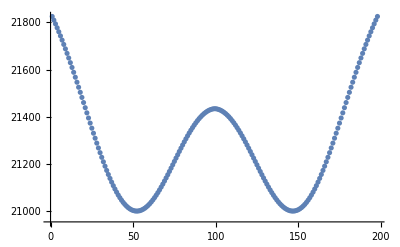
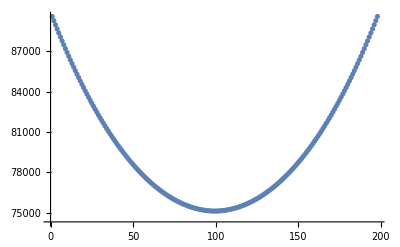

```mathematica
ListPlot[#,PlotRange->All]&/@Transpose[(Im[#]&/@#&/@(SortBy[#,Re[#]&]&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]))]
ListPlot[#]&/@Transpose[(Re[#]&/@#&/@(SortBy[#,Re[#]&]&/@Cases[vals[[All,2;;-1]],u_/;Length[u]>M]))]
```

```mathematica
freqmin=2*Pi*8;
freqmax=2*Pi*25;
num=200;
freqs=Table[freq,{freq,freqmin,freqmax,(freqmax-freqmin)/num}];
AbsoluteTiming[subharmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.1/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq],{freq,freqs}];]
AbsoluteTiming[harmonic=Table[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.1/.ρ->1/.h0->1/.ωd->freq/.ω->0.00001*freq],{freq,freqs}];]
```

{3.3093,Null}

{3.18951,Null}

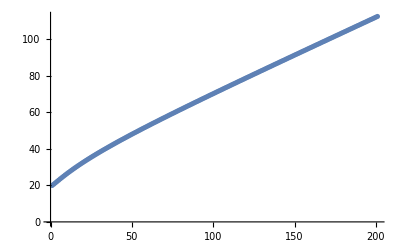
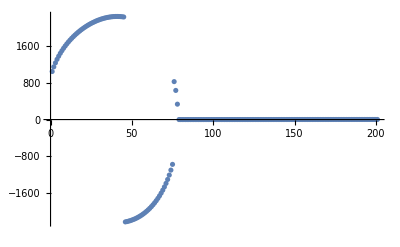
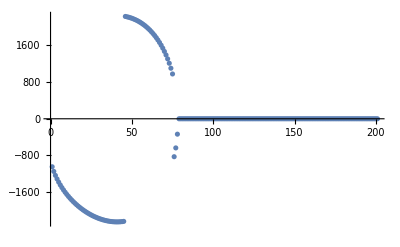
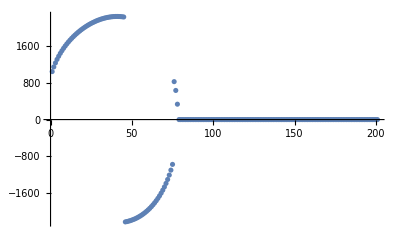
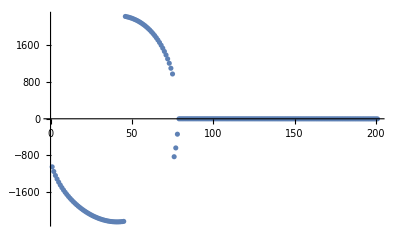
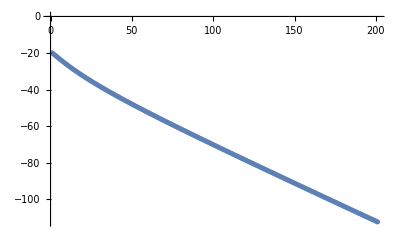
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

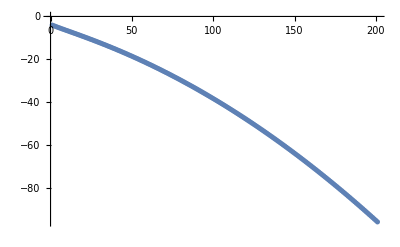
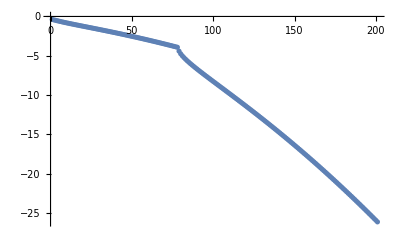
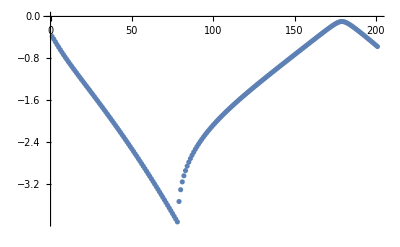
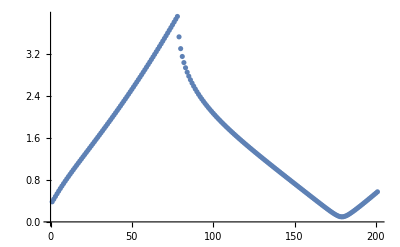
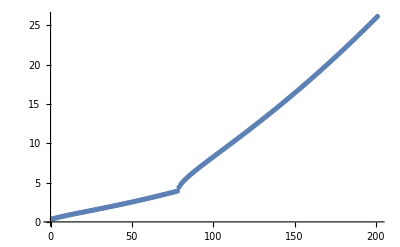
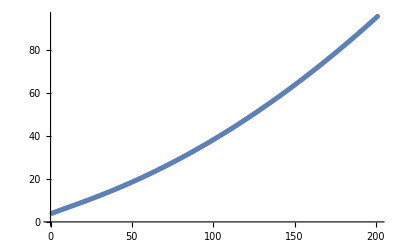
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@subharmonic])
```

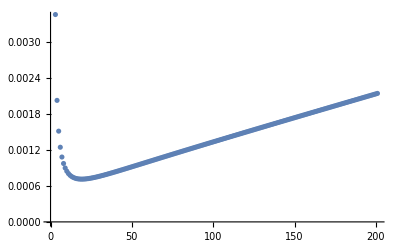
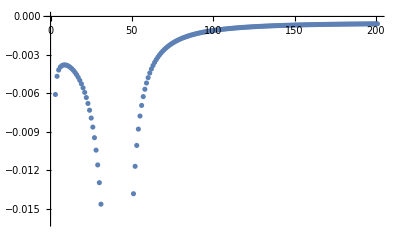
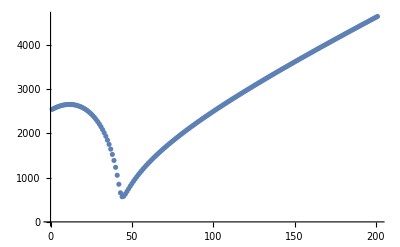
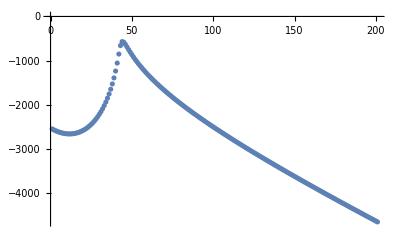
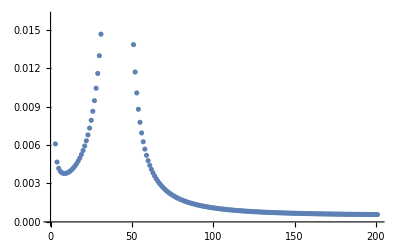
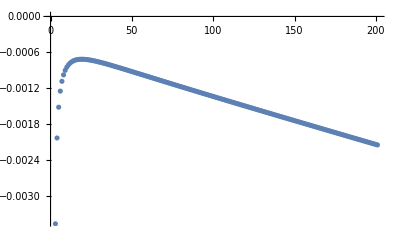
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

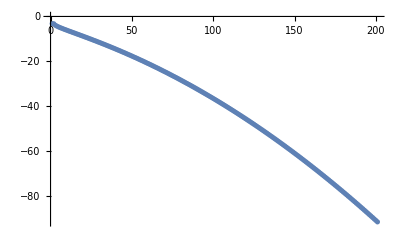
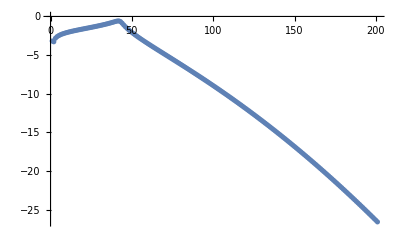
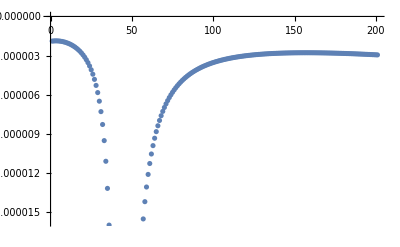
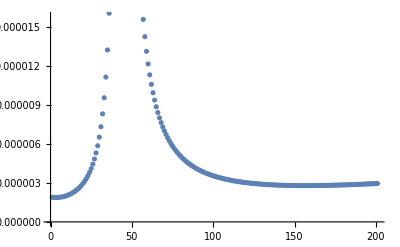
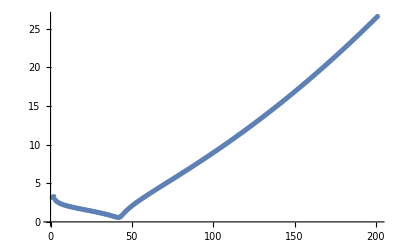
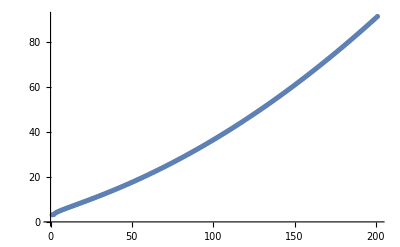
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot[Im[#]]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
ListPlot[Re[#]/980]&/@(Transpose[SortBy[#,Re[#]&]&/@harmonic])
```

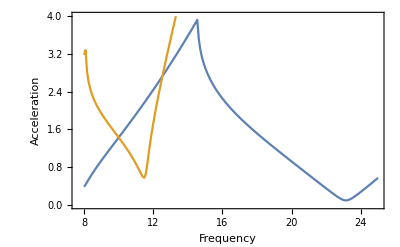

```mathematica
ListPlot[{Transpose[{freqs/(2*Pi),Re[Transpose[SortBy[#,Re[#]&]&/@subharmonic][[4]]]/980}],Transpose[{freqs/(2*Pi),Re[Transpose[SortBy[#,Re[#]&]&/@harmonic][[5]]]/980}]},PlotRange->{0,4},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]]
```

```mathematica
freqmin=2*Pi*8;
freqmax=2*Pi*25;
num=200;
length=10;
L=length/10;
freqs=Table[freq,{freq,freqmin,freqmax,(freqmax-freqmin)/num}];
AbsoluteTiming[Monitor[subharmonic2=Table[ParallelTable[Quiet[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq]],{qx,2*Pi/length,2*Pi/L,2*Pi/length}],{freq,freqs}];,N[(freq-freqmin)/(freqmax-freqmin)]]]
AbsoluteTiming[Monitor[harmonic2=Table[ParallelTable[Quiet[Eigenvalues[{eq1,eq2}/.g->980/.σ->72/.qy->0/.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.00001*freq]],{qx,2*Pi/length,2*Pi/L,2*Pi/length}],{freq,freqs}];,N[(freq-freqmin)/(freqmax-freqmin)]]]
```

{24.0759,Null}

{19.7428,Null}

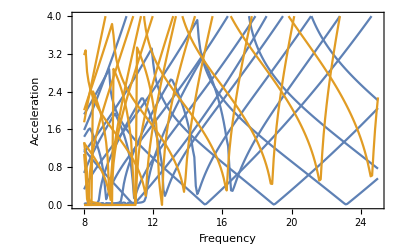

```mathematica
Show[ListPlot[Table[{#[[1]],Re[#[[2]]]/980}&/@Transpose[{freqs/(2*Pi),Transpose[SortBy[#,Re[#]&]&/@subharmonic2[[All,i]]][[4]]}],{i,1,length/L}],PlotStyle->Directive[ColorData[97,"ColorList"][[1]]],PlotRange->{0,4},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]],ListPlot[Table[{#[[1]],Re[#[[2]]]/980}&/@Transpose[{freqs/(2*Pi),Transpose[SortBy[#,Re[#]&]&/@harmonic2[[All,i]]][[5]]}],{i,1,length/L}],PlotStyle->Directive[ColorData[97,"ColorList"][[2]]],PlotRange->{0,4},Joined->True,Axes->False,Frame->True,FrameLabel->{"Frequency","Acceleration"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[1]]]]
```

```mathematica
(* The left and right eigenvectors are identical, since the flat system is symmetric *)
(* The skewedness in the eigenvectors comes from the \omega=\pm 1/2 omega_d*)
(* We need to unwind the inversion to find the 4*(2M+1)-dimensional eigenvector *)
M=5;
eq0=Simplify[(eqs0[[9;;9,9;;9]]-eqs0[[9;;9,1;;8]].Inverse[eqs0[[1;;8,1;;8]]].eqs0[[1;;8,9;;9]])[[1,1]]/.qy->0];
eq1=Table[eq0*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}];
eq2=Table[-1/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]),{l1,-M,M},{l2,-M,M}];

sys={eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]

syst={Transpose[eq1],Transpose[eq2]}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evalst,evecst}=Eigensystem[syst];]

Norm[(eq1-evals[[-1]]*eq2).evecs[[-1]]/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq]
Norm[(evecst[[-1]]).(eq1-evals[[-1]]*eq2)/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq]
```

{0.000273,Null}

{0.000268,Null}

2.43096×10^-11

2.43096×10^-11

```mathematica
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[9],5],u_/;Length[u]==5]];
Monitor[dets=Table[Det[eqs0[[1;;5,perts[[i]]]]],{i,1,Length[perts]}];,i]
DeleteDuplicates[First/@Position[dets,u_/;u≠0]]
```

{37,38,40,41,46,47,49,52,56,57,59,62,72,73,75,76,81,82,84,87,91,92,94,97,110,111,113,114,117,118,119,120,122,123,124,125}

```mathematica
M=3;
eqs2t=Transpose[Table[{0,0,0,0,0,0,0,0,-KroneckerDelta[k1,9]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]];

elim=Range[5];
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[9],Length[elim]],u_/;Length[u]==Length[elim]]];
Monitor[dets=Table[Det[eqs0[[elim,perts[[i]]]]],{i,1,Length[perts]}];,i]
lperts=DeleteDuplicates[First/@Position[dets,u_/;u≠0]]

ipert=lperts[[1]];
perts[[ipert]]
AbsoluteTiming[eqt=Simplify[(eqs0[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]]-eqs0[[Complement[Range[9],elim],perts[[ipert]]]].Inverse[eqs0[[elim,perts[[ipert]]]]].eqs0[[elim,Complement[Range[9],perts[[ipert]]]]])/.qy->0];]
Monitor[AbsoluteTiming[eq1t=ArrayFlatten[Table[eqt*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
Monitor[AbsoluteTiming[eq2t=ArrayFlatten[Table[eqs2t[[Complement[Range[9],elim],Complement[Range[9],perts[[ipert]]]]],{l1,-M,M},{l2,-M,M}]];],{l1,l2}]
```

{37,38,40,41,46,47,49,52,56,57,59,62,72,73,75,76,81,82,84,87,91,92,94,97,110,111,113,114,117,118,119,120,122,123,124,125}

{1,3,4,5,7}

{0.608607,Null}

{0.010775,Null}

{0.000673,Null}

```mathematica
syst={eq1t,eq2t}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[syst];]
evals
```

{0.000675,Null}

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-78562.2+11.4568 ⅈ,78562.2-11.4568 ⅈ,20996.9-0.192308 ⅈ,-20996.9+0.192308 ⅈ,-45.4782-7.74778×10^-13 ⅈ,45.4782-7.20383×10^-12 ⅈ}

```mathematica
M=3;
eq0=Simplify[(eqs0[[9;;9,9;;9]]-eqs0[[9;;9,1;;8]].Inverse[eqs0[[1;;8,1;;8]]].eqs0[[1;;8,9;;9]])[[1,1]]/.qy->0];
eq1=Table[eq0*KroneckerDelta[l1,l2],{l1,-M,M},{l2,-M,M}];
eq2=Table[-1/2*(KroneckerDelta[l1,l2+1]+KroneckerDelta[l1,l2-1]),{l1,-M,M},{l2,-M,M}];
```

```mathematica
freq=2*Pi*23.;
sys={eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]
evals
```

{0.000215,Null}

{ComplexInfinity,-78562.2+11.4568 ⅈ,78562.2-11.4568 ⅈ,-20996.9+0.192308 ⅈ,20996.9-0.192308 ⅈ,-45.4782+8.06057×10^-14 ⅈ,45.4782-7.73413×10^-14 ⅈ}

#### periodic

```mathematica
subs1={A->KroneckerDelta[k1,1]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],B->KroneckerDelta[k1,2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ax->KroneckerDelta[k1,3]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bx->KroneckerDelta[k1,4]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Ay->KroneckerDelta[k1,5]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],By->KroneckerDelta[k1,6]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Az->KroneckerDelta[k1,7]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2],Bz->KroneckerDelta[k1,8]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2], H->KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*KroneckerDelta[l1,l2]};
subs2={kx->qx+n1*q1.{1,0}+m1*q2.{1,0},ky->qy+n1*q1.{0,1}+m1*q2.{0,1},ω->ω+l1*ωd};
eqs1=Transpose[Table[{Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)+z Ω)]/.subs1/.subs2],Simplify[Coefficient[Expand[D[ux[x,y,z,t],x]+D[uy[x,y,z,t],y]+D[uz[x,y,z,t],z]],ⅇ^(ⅈ (kx x+ky y+t ω)-z Ω)]/.subs1/.subs2],Simplify[(I*kx*uz[x,y,z,t]-(D[ux[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs1/.subs2],Simplify[(I*ky*uz[x,y,z,t]-(D[uy[x,y,z,t],z]/.z->h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.z->h0/.subs1/.subs2],Simplify[(I*ω*(h[x,y,z,t]-h0)-uz[x,y,z,t]/.z->h0)*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,3]+KroneckerDelta[k1,4]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]-kx/ω*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,5]+KroneckerDelta[k1,6]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]-ky/ω*(KroneckerDelta[k1,1]+KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2],Simplify[KroneckerDelta[l1,l2]*((KroneckerDelta[k1,7]+KroneckerDelta[k1,8]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,Ω*as/2]*BesselI[m1-m2,Ω*as/2]+I*k/ω*(KroneckerDelta[k1,1]-KroneckerDelta[k1,2]*(-1)^(n1-n2+m1-m2))*BesselI[n1-n2,k*as/2]*BesselI[m1-m2,k*as/2])/.subs2],Simplify[(-g*(h[x,y,z,t]-h0)+(P[x,y,h0,t]+g*h0)-2*μ*(D[uz[x,y,z,t],z]/.z->h0)-σ*k^2*(h[x,y,z,t]-h0))*Exp[-I*(kx*x+ky*y+ω*t)]/.subs1]/.subs2},{k1,1,9}]]
```

{{0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0},{0,0,0,ⅈ (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0,ⅈ (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0,-√((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0},{0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2 m1,m2 n1,n2,0},{0,0,0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,ⅈ ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2 m1,m2 n1,n2,0},{-1/(ω+l1 ωd)ⅈ ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ω+l1 ωd)ⅈ ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,0,0,-ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,-ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2,ⅈ (ω+l1 ωd) l1,l2 m1,m2 n1,n2},{-1/(ω+l1 ωd)BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2,1/(ω+l1 ωd)(-1)^(1+m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qx+n1 q1.{1,0}+m1 q2.{1,0}) l1,l2,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0,0,0,0,0},{-1/(ω+l1 ωd)BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2,1/(ω+l1 ωd)(-1)^(1+m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] (qy+n1 q1.{0,1}+m1 q2.{0,1}) l1,l2,0,0,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0,0,0},{1/(ω+l1 ωd)ⅈ BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2,-1/(ω+l1 ωd)ⅈ (-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2,0,0,0,0,BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,(-1)^(m1-m2+n1-n2) BesselI[m1-m2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] BesselI[n1-n2,1/2 as √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)] l1,l2,0},{1/(ω+l1 ωd)ⅇ^(h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (ω+l1 ωd-2 ⅈ μ (qy+n1 q1.{0,1}+m1 q2.{0,1})^2-2 ⅈ μ (qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,1/(ω+l1 ωd)ⅇ^(-h0 √((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) (ω+l1 ωd-2 ⅈ μ (qy+n1 q1.{0,1}+m1 q2.{0,1})^2-2 ⅈ μ (qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,0,0,0,0,-2 ⅇ^(h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,2 ⅇ^(-h0 √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) μ √((ⅈ ρ (ω+l1 ωd))/μ+(qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2) l1,l2 m1,m2 n1,n2,-(g+σ ((qy+n1 q1.{0,1}+m1 q2.{0,1})^2+(qx+n1 q1.{1,0}+m1 q2.{1,0})^2)) l1,l2 m1,m2 n1,n2}}

```mathematica
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[1]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[1]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[2]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[2]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[3]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[3]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[4]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[4]]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[5]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[5]]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[6]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[6]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[7]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[7]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
FullSimplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[8]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-(eqs1[[8]]/.as->0)/.BesselI[a_-b_,0]:>KroneckerDelta[a,b]]
Simplify[(KroneckerDelta[l1,l2]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*eqs0[[9]]/.qx->qx+n1*q1.{1,0}+m1*q2.{1,0}/.qy->qy+n1*q1.{0,1}+m1*q2.{0,1})-eqs1[[9]]]
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0}

«6 more identical outputs»

```mathematica
eqs2=Transpose[Table[{0,0,0,0,0,0,0,0,KroneckerDelta[k1,9]*KroneckerDelta[n1,n2]*KroneckerDelta[m1,m2]*(KroneckerDelta[l1+1,l2]+KroneckerDelta[l1-1,l2])/2},{k1,1,9}]]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1/2 (-1+l1,l2+1+l1,l2) m1,m2 n1,n2}}

```mathematica
perts=DeleteDuplicates[Sort/@Cases[Permutations[Range[9],5],u_/;Length[u]==5]];
Monitor[dets=Table[Det[eqs1[[1;;5,perts[[i]]]]],{i,1,Length[perts]}];,i]
DeleteDuplicates[First/@Position[dets,u_/;u≠0]]
```

{37,38,40,41,46,47,49,52,56,57,59,62,72,73,75,76,81,82,84,87,91,92,94,97,110,111,113,114,117,118,119,120,122,123,124,125}

```mathematica
perts[[37]]
```

{1,3,4,5,7}

```mathematica
M=3;
M2=3;
AbsoluteTiming[eq=Simplify[(eqs1[[6;;9,Complement[Range[9],perts[[37]]]]]-eqs1[[6;;9,perts[[37]]]].Inverse[eqs1[[1;;5,perts[[37]]]]].eqs1[[1;;5,Complement[Range[9],perts[[37]]]]])/.qy->0];]
Monitor[AbsoluteTiming[eq1=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[eq,{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
Monitor[AbsoluteTiming[eq2=ArrayFlatten[ArrayFlatten[ArrayFlatten[Table[eqs2[[6;;9,Complement[Range[9],perts[[37]]]]],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2},{l1,-M,M},{l2,-M,M}]]]];],{n1,n2,m1,m2,l1,l2}]
```

{5.93095,Null}

{113.839,Null}

{1.26283,Null}

```mathematica
Dimensions[eq1]
```

{1372,1372}

```mathematica
(* Eigenvalues for square lattice with qx=ks/2 *)
q1=2*Pi*{1,0};
q2=2*Pi*{0,1};

freq=2*Pi*23.;
sys={eq1,eq2}/.g->980/.σ->72/.qy->0/.qx->2*Pi/2./.μ->0.01/.ρ->1/.h0->1/.ωd->freq/.ω->0.5*freq;
AbsoluteTiming[{evals,evecs}=Eigensystem[sys];]
evals
```

General::munfl: (-2.92315×10^-69+6.69165×10^-70 ⅈ) (1.92716×10^-245+8.31025×10^-246 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.92315×10^-69+6.69165×10^-70 ⅈ) (-1.58872×10^-285+1.00461×10^-285 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.58872×10^-285+1.00461×10^-285 ⅈ) (-2.92315×10^-69+6.69165×10^-70 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

### Thin film

```mathematica
Clear[σ]
Clear[ρ]
Clear[μ]
H[x_,t_]:=H0+h*Exp[I*k*x+I*s*t]
Hs[x_]:=As*Sin[ks*x];
```

```mathematica
mat=FullSimplify[Table[Expand[TrigToExp[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]]]/.Exp[u_]:>Exp[Expand[u]]/.Exp[a_]:>0,{n,-3,3},{m,-1,1}]/.h->1]
```

{{-(ad As^3 k (k-3 ks) ρ)/(48 μ),(ⅈ As^3 k (k-3 ks) (g ρ+k^2 σ))/(24 μ),(ad As^3 k (k-3 ks) ρ)/(48 μ)},{-(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ),-(As^2 H0 k (k-2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k-2 ks) ρ)/(8 μ)},{(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ),-(ⅈ As (As^2+4 H0^2) k (k-ks) (g ρ+k^2 σ))/(8 μ),-(ad As (As^2+4 H0^2) k (k-ks) ρ)/(16 μ)},{(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ),ⅈ s+(H0 (3 As^2+2 H0^2) k^2 (g ρ+k^2 σ))/(6 μ),-(ⅈ ad (3 As^2 H0+2 H0^3) k^2 ρ)/(12 μ)},{-(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ),(ⅈ As (As^2+4 H0^2) k (k+ks) (g ρ+k^2 σ))/(8 μ),(ad As (As^2+4 H0^2) k (k+ks) ρ)/(16 μ)},{-(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ),-(As^2 H0 k (k+2 ks) (g ρ+k^2 σ))/(4 μ),(ⅈ ad As^2 H0 k (k+2 ks) ρ)/(8 μ)},{(ad As^3 k (k+3 ks) ρ)/(48 μ),-(ⅈ As^3 k (k+3 ks) (g ρ+k^2 σ))/(24 μ),-(ad As^3 k (k+3 ks) ρ)/(48 μ)}}

```mathematica
n=-2;
m=1;
AbsoluteTiming[Simplify[h*mat[[n+4,m+2]]/(Integrate[Exp[-I*(k+n*ks)*x]*Exp[-I*(s+m*ωd)*t]*Evaluate[Normal[Series[D[H[x,t],t]+D[(H[x,t]-Hs[x])^3/3*D[σ/μ*D[H[x,t],{x,2}]-H[x,t]*ρ/μ*(g+ad*Sin[ωd*t]),x], x],{h,0,1}]]],{x,0,2*Pi/ks},{t,0,2*Pi/ωd}]/(2*Pi/ks)/(2*Pi/ωd))]]
```

{59.808,1}

```mathematica
μ=10^-3;
ρ=1;
σ=72;
g=980;
H0=0.1;
As=0.8*H0;
M2=5;
A[k_,ks_,ad_]=-ArrayFlatten[-I*Table[If[Abs[n1-n2]<=3&&Abs[m1-m2]<=1,(mat[[n1-n2+4,m1-m2+2]]/.k->k-n1*ks),0],{n1,-M2,M2},{n2,-M2,M2},{m1,-M2,M2},{m2,-M2,M2}]/.s->0];
```

```mathematica
Dimensions[A[k,ks,ad]]
```

{121,121}

```mathematica
A[k,ks,ad]
```

{{(0.+0.653333 ⅈ) (980+72 (k-5 ks)^2) (k-5 ks)^2,(-0.326667+0. ⅈ) ad (k-5 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (980+72 (k-4 ks)^2) (k-5 ks) (k-4 ks),(0.+0.232 ⅈ) ad (k-5 ks) (k-4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (980+72 (k-3 ks)^2) (k-5 ks) (k-3 ks),(0.08+0. ⅈ) ad (k-5 ks) (k-3 ks),0,0,0,0,0,0,0,0,0,55,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},119,{0,119,1}}
 |  |  |  |

```mathematica
A[k,ks,ad][[12]]
```

{(-0.464+0. ⅈ) (k+4 ks) (k+5 ks) (980+72 (k+4 ks)^2),(0.-0.232 ⅈ) ad (k+4 ks) (k+5 ks),0,0,0,0,0,0,0,0,0,(0.+0.653333 ⅈ) (k+4 ks)^2 (980+72 (k+4 ks)^2),(-0.326667+0. ⅈ) ad (k+4 ks)^2,0,0,0,0,0,0,0,0,0,(0.464+0. ⅈ) (k+3 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.+0.232 ⅈ) ad (k+3 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(0.-0.16 ⅈ) (k+2 ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.08+0. ⅈ) ad (k+2 ks) (k+4 ks),0,0,0,0,0,0,0,0,0,(-0.0213333+0. ⅈ) (k+ks) (k+4 ks) (980+72 (k+4 ks)^2),(0.-0.0106667 ⅈ) ad (k+ks) (k+4 ks),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

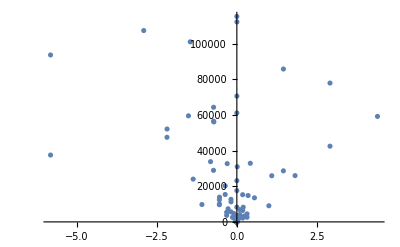

```mathematica
ListPlot[{Re[#],Im[#]}&/@Eigenvalues[A[0.5,1.0, 1000]],PlotRange->All]
```

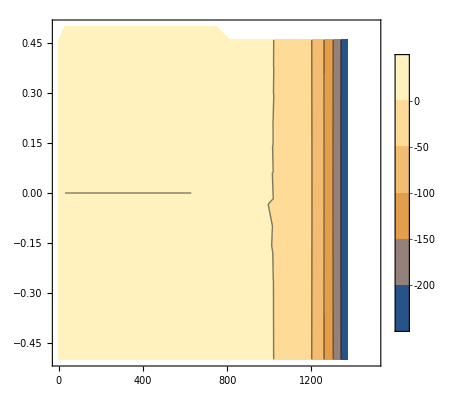

```mathematica
num=50;
Monitor[
vals=Table[{ad,k,MinimalBy[{Re[#],Im[#]}&/@Eigenvalues[A[k,1.0,ad]],#[[2]]&][[1,2]]},{ad,0,1500,1500/num},{k,-1/2,1/2,1.0/num}];,{ad,k}]
ListContourPlot[Flatten[vals,1],PlotLegends->True]
```

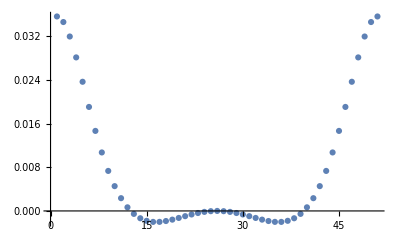

```mathematica
ListPlot[vals[[num/2+10,All,3]]]
```

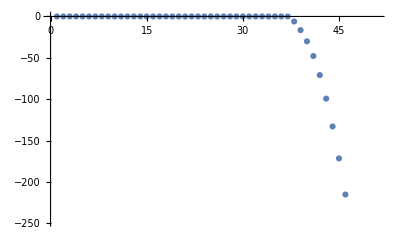

```mathematica
ListPlot[vals[[All,num/2+1,3]]]
```